```mathematica
V[r_]=-(1/r)-(1.0415223038416566 E^(-0.9990999998788636 r))/r;α=2.;
```

```mathematica
Get["C:\\Users\\ASUS\\Documents\\TestDump_efHQ.mx"]
```

```mathematica
Module[{shift=10,d=2000,n=20,ev,evShifted},{ev,ef}=NDEigensystem[{shift f[r]+V[r] f[r]-1/α f''[r](*+NeumannValue[0,r==d]*),DirichletCondition[f[r]==0,True]},f[r],{r,0,d},n,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.001}}},"Eigensystem"->{"Arnoldi",MaxIterations->Infinity}}];
evShifted=ev-shift]
```

{-1.33732,-0.186434,-0.0710575,-0.0374072,-0.023051,-0.0156184,-0.0112778,-0.00852433,-0.00666881,-0.00535929,-0.0044008,-0.00367822,-0.00312003,-0.0026799,-0.00232673,-0.00203904,-0.00180159,-0.00160333,-0.00143608,-0.0012937}

```mathematica
Table[NIntegrate[Laplacian[ef[[i]],{r}]^2,{r,0,2000},WorkingPrecision->20],{i,6}]
```

NIntegrate::ncvb: 在接近 {r} = {0.1127030230027328894846448018202193378156315838220179400570623135295232} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 75.04712509602504002988743936332564802889986833189311524324653625000794 和 0.03247863569799793651411580296248686464151011549531274619693142039304984.

NIntegrate::ncvb: 在接近 {r} = {0.1127030230027328894846448018202193378156315838220179400570623135295232} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 5.897731337244297320244974962366363062031019002598467484092252317159525 和 0.002076328006843794310359434388105211863785506286042459792870160188780572.

NIntegrate::ncvb: 在接近 {r} = {0.1127030230027328894846448018202193378156315838220179400570623135295232} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 1.383827527285600037322024562882250550547821054966241270216319490704163 和 0.0004624909346818281408430617127379089906642082741336173361072804453879094.

General::stop: 在本次计算中，NIntegrate::ncvb 的进一步输出将被抑制.

{75.04712509602504003,5.8977313372442973202,1.3838275272856000373,0.53351847484452425958,0.25967637445450231166,0.14543380637569422279}

```mathematica
{75.06762659610097063527793960468755094728`20.,5.8983157686756864244343783028219462036`20.,1.3839198652475268494054875033108069673441558825343560480806`20.,0.5335529621107729103440340820144061583664264393992945987484`20.,5.509846564687439816334492316876960354475750112384484015011`20.*^269,3.253106607945993974470256913381324510265239806509301211291`20.*^269}
```

{75.067626596100970635,5.8983157686756864244,1.3839198652475268494,0.53355296211077291034,5.5098465646874398163×10^269,3.2531066079459939745×10^269}

```mathematica
NIntegrate[Laplacian[ef[[6]][r],{r}]^2,{r,0,∞},WorkingPrecision->20,MaxRecursion->20]
```

NIntegrate::inumr: 在以 {{0.,3.0716729249965974834×10^445}} 为界的区域内，对于所有采样点，计算被积函数 (InterpolatingFunction[{{0.,2000.}},{5,4225,0,{4000001},{3},{2},0,0,0,Automatic,{},{},False},{«23»[«1»]},{0.,«49»,«3999951»},{Automatic}][r])^2 得到非数值.

NIntegrate[(ef⟦6⟧[r]{r})^2,{r,0,∞},WorkingPrecision→20,MaxRecursion→20]

```mathematica
ef
```

{InterpolatingFunction[{{0., 2000.}}, <>],InterpolatingFunction[{{0., 2000.}}, <>],InterpolatingFunction[{{0., 2000.}}, <>],InterpolatingFunction[{{0., 2000.}}, <>],InterpolatingFunction[{{0., 2000.}}, <>],InterpolatingFunction[{{0., 2000.}}, <>],InterpolatingFunction[{{0., 2000.}}, <>],InterpolatingFunction[{{0., 2000.}}, <>],InterpolatingFunction[{{0., 2000.}}, <>],InterpolatingFunction[{{0., 2000.}}, <>],InterpolatingFunction[{{0., 2000.}}, <>],InterpolatingFunction[{{0., 2000.}}, <>],InterpolatingFunction[{{0., 2000.}}, <>],InterpolatingFunction[{{0., 2000.}}, <>],InterpolatingFunction[{{0., 2000.}}, <>],InterpolatingFunction[{{0., 2000.}}, <>],InterpolatingFunction[{{0., 2000.}}, <>],InterpolatingFunction[{{0., 2000.}}, <>],InterpolatingFunction[{{0., 2000.}}, <>],InterpolatingFunction[{{0., 2000.}}, <>]}

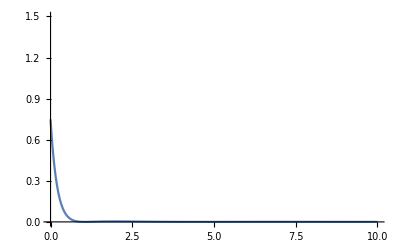

```mathematica
Plot[Evaluate[Laplacian[ef[[6]][r],{r}]^2],{r,0,10},PlotRange->{0,1.5}]
```

```mathematica
Evaluate[Laplacian[ef[[5]],{r}]^2]/.r->0
```

1.34259